```mathematica
m=4

sbox="E4D12FB83A6C5907";
S[x_]:=IntegerDigits[FromDigits[sbox,16],16,16][[x+1]]
```

4

```mathematica
S[0]
```

14

```mathematica
delta=11
S[delta]
```

11

S[11]

```mathematica
NL[alpha_,beta_]:=2^m-Sum[Mod[DigitCount[BitAnd[alpha,x],2,1] +DigitCount[BitAnd[beta,S[x]],2,1],2],{x,0,2^m-1}]
```

```mathematica
Table[2 bias[a,b],{a,0,2^m-1},{b,0,2^m-1}]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/4 | -1/4 | 0 | 0 | -1/4 | 3/4 | 1/4 | 1/4 | 0 | 0 | 1/4 | 1/4 | 0 | 0
0 | 0 | -1/4 | -1/4 | 0 | 0 | -1/4 | -1/4 | 0 | 0 | 1/4 | 1/4 | 0 | 0 | -3/4 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | -3/4 | -1/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/4
0 | 1/4 | 0 | -1/4 | -1/4 | -1/2 | -1/4 | 0 | 0 | -1/4 | 0 | 1/4 | 1/4 | -1/2 | 1/4 | 0
0 | -1/4 | -1/4 | 0 | -1/4 | 0 | 1/2 | 1/4 | -1/4 | 0 | -1/2 | 1/4 | 0 | -1/4 | -1/4 | 0
0 | 1/4 | -1/4 | 1/2 | 1/4 | 0 | 0 | 1/4 | 0 | -1/4 | 1/4 | 1/2 | -1/4 | 0 | 0 | -1/4
0 | -1/4 | 0 | 1/4 | 1/4 | -1/2 | 1/4 | 0 | -1/4 | 0 | 1/4 | 0 | 1/2 | 1/4 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | -1/4 | -3/4
0 | 0 | -1/4 | -1/4 | 0 | 0 | -1/4 | -1/4 | -1/2 | 0 | -1/4 | 1/4 | 0 | 1/2 | 1/4 | -1/4
0 | 1/2 | -1/4 | 1/4 | -1/2 | 0 | 1/4 | -1/4 | 1/4 | 1/4 | 0 | 0 | 1/4 | 1/4 | 0 | 0
0 | 1/2 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/4 | 1/2 | -1/4 | -1/4 | 0 | 1/4 | 0 | 1/4 | 0 | 1/4 | 1/2 | 0 | 1/4 | 0 | -1/4
0 | 1/4 | 1/4 | 0 | -1/4 | 1/2 | 0 | 1/4 | -1/2 | -1/4 | 1/4 | 0 | 1/4 | 0 | 0 | 1/4
0 | 1/4 | 1/4 | 0 | -1/4 | -1/2 | 0 | 1/4 | -1/4 | 0 | 0 | -1/4 | -1/2 | 1/4 | -1/4 | 0
0 | -1/4 | -1/2 | -1/4 | -1/4 | 0 | 1/4 | 0 | 0 | -1/4 | 1/2 | -1/4 | -1/4 | 0 | 1/4 | 0

```mathematica
LAT[a_,b_]:=NL[a,b]-2^(m-1)
bias[a_,b_]:=LAT[a,b]/2^m
cor[a_,b_]:=2bias[a,b]
```

```mathematica
NL[a_]:=Table[NL[a,b],{b,0,2^m-1}]
```

```mathematica
LAT[a_]:=Table[{a,b,LAT[a,b]},{b,0,2^m-1}]
```

```mathematica
HW[x_]:=DigitCount[x,2,1]
```

```mathematica
HW[0]
```

0

```mathematica
(* criterio per selezionare : bias non nullo e una sola box attiva (criterio minimale) *)
TestChar[entry_]:=(entry[[3]]=!=0)&&(HW[entry[[2]]]==1)

SparseLAT[]:=Flatten[Table[Map[{#[[1]],#[[2]]}+1->#[[3]]&,
Select[LAT[alpha],TestChar]
],
{alpha,0,2^m-1}],1]
```

```mathematica
MakeEdge[inputmask_]:=(
(*Print[inputmask];*)
chars=Select[SparseLAT[],#[[1,1]]==inputmask[[2]]+1&];
If[chars=!={},
max=Max[weights=Map[#[[2]]&,chars]];
outmask=chars[[Position[weights,max][[1,1]]]];
permutedmask=Reverse[{inputmask[[1]],1+Log[2,outmask[[1,2]]-1]}];
{inputmask,permutedmask,outmask[[2]]},
{}]
)

ExtendEdge[edge_]:=MakeEdge[edge[[2]]]
```

{2,12}

{{{1,1},{4,1},2},{{1,2},{2,1},-2},{{1,3},{4,1},2},{{1,4},{1,1},2},{{1,5},{1,1},-2},{{1,6},{1,1},2},{{1,7},{3,1},2},{{1,8},{4,1},-2},{{1,9},{2,1},-2},{{1,10},{1,1},4},{{1,11},{1,1},4},{{1,12},{2,1},4},{{1,13},{1,1},2},{{1,14},{1,1},2},{{1,15},{1,1},-2},{},{{2,1},{4,2},2},{{2,2},{2,2},-2},{{2,3},{4,2},2},{{2,4},{1,2},2},{{2,5},{1,2},-2},{{2,6},{1,2},2},{{2,7},{3,2},2},{{2,8},{4,2},-2},{{2,9},{2,2},-2},{{2,10},{1,2},4},{{2,11},{1,2},4},{{2,12},{2,2},4},{{2,13},{1,2},2},{{2,14},{1,2},2},{{2,15},{1,2},-2},{},{{3,1},{4,3},2},{{3,2},{2,3},-2},{{3,3},{4,3},2},{{3,4},{1,3},2},{{3,5},{1,3},-2},{{3,6},{1,3},2},{{3,7},{3,3},2},{{3,8},{4,3},-2},{{3,9},{2,3},-2},{{3,10},{1,3},4},{{3,11},{1,3},4},{{3,12},{2,3},4},{{3,13},{1,3},2},{{3,14},{1,3},2},{{3,15},{1,3},-2},{},{{4,1},{4,4},2},{{4,2},{2,4},-2},{{4,3},{4,4},2},{{4,4},{1,4},2},{{4,5},{1,4},-2},{{4,6},{1,4},2},{{4,7},{3,4},2},{{4,8},{4,4},-2},{{4,9},{2,4},-2},{{4,10},{1,4},4},{{4,11},{1,4},4},{{4,12},{2,4},4},{{4,13},{1,4},2},{{4,14},{1,4},2},{{4,15},{1,4},-2},{}}

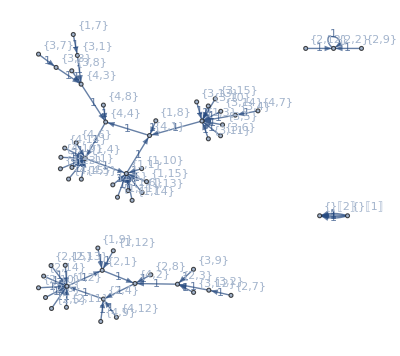

```mathematica
inputmask={2,12}
X=Map[MakeEdge,Tuples[{{1,2,3,4},Range[1,16]}]]
G=Graph[Map[DirectedEdge[#[[1]],#[[2]]]&,X],VertexLabels->Automatic,EdgeLabels->"EdgeWeight"]
```

{{{1,2}->{2,1},{2,1}->{4,2},{4,2}->{2,4},{2,4}->{1,2}},{{1,1}->{4,1},{4,1}->{4,4},{4,4}->{1,4},{1,4}->{1,1}}}

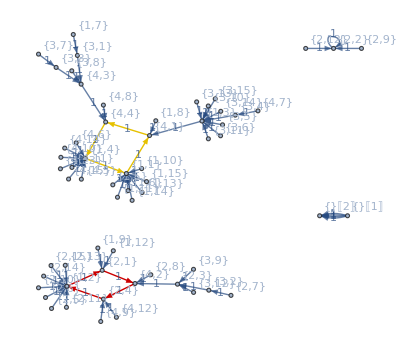

```mathematica
cycles=FindCycle[G,Infinity,Infinity]
HighlightGraph[G,cycles]
```

```mathematica
MakeEdge[{2,13}]
MakeEdge[{1,2}]
MakeEdge[{2,1}]
MakeEdge[{4,2}]
MakeEdge[{2,4}]
```

{{2,13},{1,2},2}

{{1,2},{2,1},-2}

{{2,1},{4,2},2}

{{4,2},{2,4},-2}

{{2,4},{1,2},2}

{{2,13},{1,2},2}

{{1,2},{2,1},-2}

{{2,1},{4,2},2}

{{4,2},{2,4},-2}

{{2,4},{1,2},2}

```mathematica
MakeEdge[{2,16}]
```

{2,16}

{}

```mathematica
chars=Select[SparseLAT[],#1⟦1,1⟧=={2,16}⟦2⟧+1&]
```

{}

{1,1}

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{1,7}

{1,8}

{1,9}

{1,10}

{1,11}

{1,12}

{1,13}

{1,14}

{1,15}

{1,16}

{2,1}

{2,2}

{2,3}

{2,4}

{2,5}

{2,6}

{2,7}

{2,8}

{2,9}

{2,10}

{2,11}

{2,12}

{2,13}

{2,14}

{2,15}

{2,16}

{3,1}

{3,2}

{3,3}

{3,4}

{3,5}

{3,6}

{3,7}

{3,8}

{3,9}

{3,10}

{3,11}

{3,12}

{3,13}

{3,14}

{3,15}

{3,16}

{4,1}

{4,2}

{4,3}

{4,4}

{4,5}

{4,6}

{4,7}

{4,8}

{4,9}

{4,10}

{4,11}

{4,12}

{4,13}

{4,14}

{4,15}

{4,16}

{{{1,1},{4,1},2},{{1,2},{2,1},-2},{{1,3},{4,1},2},{{1,4},{1,1},2},{{1,5},{1,1},-2},{{1,6},{1,1},2},{{1,7},{3,1},2},{{1,8},{4,1},-2},{{1,9},{2,1},-2},{{1,10},{1,1},4},{{1,11},{1,1},4},{{1,12},{2,1},4},{{1,13},{1,1},2},{{1,14},{1,1},2},{{1,15},{1,1},-2},{},{{2,1},{4,2},2},{{2,2},{2,2},-2},{{2,3},{4,2},2},{{2,4},{1,2},2},{{2,5},{1,2},-2},{{2,6},{1,2},2},{{2,7},{3,2},2},{{2,8},{4,2},-2},{{2,9},{2,2},-2},{{2,10},{1,2},4},{{2,11},{1,2},4},{{2,12},{2,2},4},{{2,13},{1,2},2},{{2,14},{1,2},2},{{2,15},{1,2},-2},{},{{3,1},{4,3},2},{{3,2},{2,3},-2},{{3,3},{4,3},2},{{3,4},{1,3},2},{{3,5},{1,3},-2},{{3,6},{1,3},2},{{3,7},{3,3},2},{{3,8},{4,3},-2},{{3,9},{2,3},-2},{{3,10},{1,3},4},{{3,11},{1,3},4},{{3,12},{2,3},4},{{3,13},{1,3},2},{{3,14},{1,3},2},{{3,15},{1,3},-2},{},{{4,1},{4,4},2},{{4,2},{2,4},-2},{{4,3},{4,4},2},{{4,4},{1,4},2},{{4,5},{1,4},-2},{{4,6},{1,4},2},{{4,7},{3,4},2},{{4,8},{4,4},-2},{{4,9},{2,4},-2},{{4,10},{1,4},4},{{4,11},{1,4},4},{{4,12},{2,4},4},{{4,13},{1,4},2},{{4,14},{1,4},2},{{4,15},{1,4},-2},{}}

-Graphics-

{{{2,13},{1,2},2},{{1,2},{2,1},-2},{{2,1},{4,2},2},{{4,2},{2,4},-2},{{2,4},{1,2},2},{{1,2},{2,1},-2}}

```mathematica
chars
```

{{3,3}→-2}

```mathematica
outmask
```

{{3,3}→-2}

```mathematica
permutedmask
```

{1+(ⅈ π+Log[3])/Log[2],2}

```mathematica
weights
```

{-2}

```mathematica
Log[2,outmask[[1,2]]-1]
```

1

```mathematica
BitIndex[box_,bit_]:=4(box-1)+Log[2,bit]
```

```mathematica
BitIndex[2,2]
```

5

```mathematica
BitIndex[inputmask[[1]],outmask[[1,2]]-1]
```

5

```mathematica
?P
```

Missing[UnknownSymbol,P]

```mathematica
Normal[SparseArray[SparseLAT[]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 2 | 0 | 0 | -2 | 0 | 0 | 0 | 0
0 | -2 | -2 | 0 | -2 | 0 | 0 | 0 | -2
0 | 2 | -2 | 0 | 2 | 0 | 0 | 0 | 0
0 | -2 | 0 | 0 | 2 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2
0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | -4
0 | 4 | -2 | 0 | -4 | 0 | 0 | 0 | 2
0 | 4 | 0 | 0 | 4 | 0 | 0 | 0 | 0
0 | -2 | 4 | 0 | -2 | 0 | 0 | 0 | 2
0 | 2 | 2 | 0 | -2 | 0 | 0 | 0 | -4
0 | 2 | 2 | 0 | -2 | 0 | 0 | 0 | -2
0 | -2 | -4 | 0 | -2 | 0 | 0 | 0 | 0)

-Graphics-

```mathematica
inputmask={2,12}
```

{0,12,0,0}

```mathematica
DDT[delta_]:=(
Delta=Table[BitXor[S[BitXor[x,delta]],S[x]],{x,0,15}];
Map[{delta,#}+1->Count[Delta,#]&,Union[Delta]]
)
```

```mathematica
DDT[]:=Drop[Flatten[Table[DDT[delta],{delta,0,15}],1],1]
```

```mathematica
DDT[]
```

{{2,4}→2,{2,8}→2,{2,10}→2,{2,11}→4,{2,13}→4,{2,14}→2,{3,4}→2,{3,6}→6,{3,7}→2,{3,8}→2,{3,10}→2,{3,15}→2,{4,3}→2,{4,5}→2,{4,10}→4,{4,11}→2,{4,13}→2,{4,16}→4,{5,4}→2,{5,7}→6,{5,10}→2,{5,12}→4,{5,13}→2,{6,2}→4,{6,6}→2,{6,7}→2,{6,11}→4,{6,13}→2,{6,16}→2,{7,4}→4,{7,6}→4,{7,13}→2,{7,14}→2,{7,15}→2,{7,16}→2,{8,3}→2,{8,4}→2,{8,5}→2,{8,7}→2,{8,10}→2,{8,11}→2,{8,16}→4,{9,7}→2,{9,8}→2,{9,12}→4,{9,14}→4,{9,15}→2,{9,16}→2,{10,2}→2,{10,5}→2,{10,8}→4,{10,9}→2,{10,11}→2,{10,12}→2,{10,13}→2,{11,2}→2,{11,3}→2,{11,9}→6,{11,12}→2,{11,15}→4,{12,3}→8,{12,6}→2,{12,8}→2,{12,14}→2,{12,16}→2,{13,2}→2,{13,5}→2,{13,6}→2,{13,7}→2,{13,12}→2,{13,14}→6,{14,2}→4,{14,8}→4,{14,9}→2,{14,11}→2,{14,13}→2,{14,15}→2,{15,3}→2,{15,4}→4,{15,5}→2,{15,9}→6,{15,15}→2,{16,2}→2,{16,5}→6,{16,10}→4,{16,12}→2,{16,15}→2}

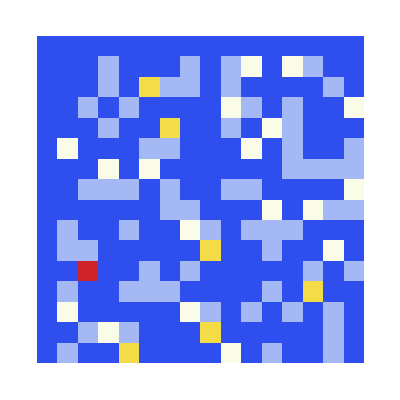

```mathematica
ArrayPlot[SparseArray[DDT[]],ColorFunction->"TemperatureMap"]
```

```mathematica
SparseArray[DDT[]]//MatrixForm
```

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 4 | 0 | 4 | 2 | 0 | 0
0 | 0 | 0 | 2 | 0 | 6 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 4 | 2 | 0 | 2 | 0 | 0 | 4
0 | 0 | 0 | 2 | 0 | 0 | 6 | 0 | 0 | 2 | 0 | 4 | 2 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 4 | 0 | 2 | 0 | 0 | 2
0 | 0 | 0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2
0 | 0 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 4 | 0 | 4 | 2 | 2
0 | 2 | 0 | 0 | 2 | 0 | 0 | 4 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0
0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 2 | 0 | 0 | 4 | 0
0 | 0 | 8 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2
0 | 2 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 6 | 0 | 0
0 | 4 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0
0 | 0 | 2 | 4 | 2 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 2 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 4 | 0 | 2 | 0 | 0 | 2 | 0)

```mathematica
DDT[0]
DDT[delta]
```

```mathematica
HW[x_]:=Plus@@IntegerDigits[x,2]
```

```mathematica
selectedchars=Select[DDT[delta],0<HW[#[[1,2]]-1]<=2&]
```

{{12,3}→8,{12,6}→2}

```mathematica
i=2
```

2

```mathematica
dchar=selectedchars[[2]]
{{i,delta},P[{0,dchar[[1,2]]-1,0,0}],dchar[[2]]/2^4}
```

{12,6}→2

{{2,11},{0,4,0,4},1/8}

```mathematica
array={0,4,2,4};
tmp=Map[{#,Flatten@Position[array,#]}&,Union@Select[array,#>0&]]

ff[x_]:=Map[{#,x[[1]]}&,x[[2]]]

Map[ff,tmp]
```

{{2,{3}},{4,{2,4}}}

{{{3,2}},{{2,4},{4,4}}}

```mathematica
ff[{2,{3}}]
```

{{3,2}}

```mathematica
permutation={1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}
```

```mathematica
P[box_,indice_]:={indice,box}
```